Multi-Control NOT Gate |

The Toffoli Gatepaclet:Q3/tutorial/MultiControlNOTGate#770299810 | Implementationspaclet:Q3/tutorial/MultiControlNOTGate#1310796799
The Fredkin Gatepaclet:Q3/tutorial/MultiControlNOTGate#1991838106 |

See also Section 2.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

The multi - control NOT gate is similar to the CNOT gate on two qubits, but it is controlled by a register of multiple qubits rather than by a single qubit . Let c≡c_1 c_2(⋯c)_n and t be the computational basis states of the control register and the target qubit, respectively . Under the multi-control NOT gate, they transform as

c⊗t↦c⊗(c_1 c_2(⋯c)_n)⊕t

or  equivalently,

c⊗t↦c⊗(X^(c_1 c_2(⋯c)_n)t)

The logical bit value of the target qubit flips if and only if every qubit in the control register is set to |1⟩. In the quantum circuit model, a multi-control NOT gate is depicted as

Evidently, the multi-control NOT gate is a special case of the multi-control unitary gates, but it is worth a separate discussion for a couple of reasons. First of all, efficient implementations of multi-control unitary gate heavily rely on implementation of the multi-control NOT gate. Furthermore, the multi-control NOT gate plays a key role when one converts the two-level unitary transformation on more than two qubits. This is due to the column and row exchange feature of the multi-control NOT gate.

CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | The controlled-NOT or CNOT gate
Toffolipaclet:Q3/ref/ToffoliQ3 Package Symbol | The Toffoli gate
Fredkinpaclet:Q3/ref/FredkinQ3 Package Symbol | The Fredkin gate
Deutschpaclet:Q3/ref/DeutschQ3 Package Symbol | The Deutsch gate
ControlledUpaclet:Q3/ref/ControlledUQ3 Package Symbol | Controlled-unitary gates

Multi-control unitary gates available in Q3.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this documentation, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

The Toffoli Gate

Let us start with the Toffoli gate, the simplest of the multi-control NOT gate with two qubits in the control register,

.

This gate is important since all widely-known implementations of multi-control NOT gates with a larger control register are built upon the Toffoli gate. The Toffoli gate has attracted interest because it is universal for classical reversible computation. Unfortunately, however, it is not universal for quantum computation.

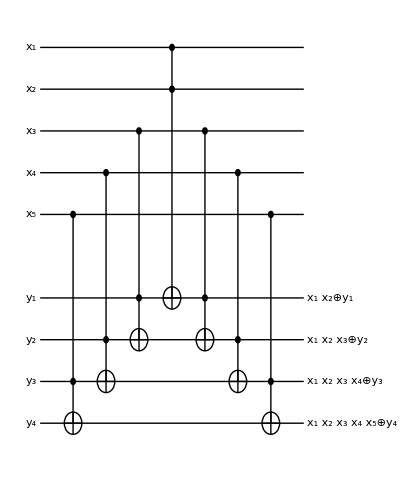

Figure 1. A quantum circuit to get the cumulative products of bit values of qubits.

An interesting application of the Toffoli gate is to achieve the cumulative products (or bit-wise AND) of the bit values of qubits (to be compared with the sum (or bit-wise OR) of bit values using the CNOT gate). Consider a control register of n qubits and a target register of n−1 qubits, and denote the respective computational basis states by x_1,x_2,⋯,x_n and y_1,y_2,⋯,y_(n-1). Combine the Toffoli gates consecutively as in Figure 1. By definition of the Toffoli gate, the logical value y_1 of the first target qubit is flipped if and only if both the first and second control qubit are set to |1⟩, that is, x_1 x_2=1. On the other hand, y_2 is flipped only when the first three qubits in the control register are all set to |1⟩, i.e., x_1 x_2 x_3=1. This pattern continues down the target register so that

y_k↦x_1 x_2(⋯x)_n⊕y_k

for k=1,2,…, n-1 as in Figure 1. This feature of the Toffoli gate provides a powerful method to efficiently implement multi-control NOT gates with a larger control register (see below).

Apparently, the Toffoli gate is a three-qubit unitary gate. How can one implement it using only single-qubit or two-qubit elementary gates? Consider the quantum circuit in Figure 2 consisting of two CNOT gates and a controlled-unitary gate,

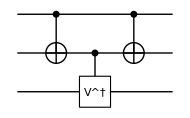
-Graphics-.

Figure 2. Conditional-unitary gate. The unitary operator V^† takes effects only if either (but not both) of the first and second qubit is set to 1.

The unitary operator V^† takes effect only when either (but not both) of the two control qubits is set to |1⟩. Therefore, combining this quantum circuit with two controlled-V gates controlled by the first and second control qubit, respectively, leads to the two-control V^2 gate, where V^2 operates only when both control qubits are set to |1⟩, as in Figure 3.

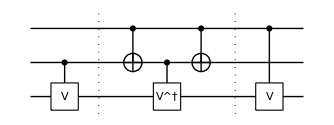
-Graphics-=

Figure 3. An implementation of the Toffoli gate based on the conditional-unitary gate with V=√X.

Therefore, putting V=√X, the quantum circuit on the left-hand side reproduces the Toffoli gate. Here we have chosen a combination in the particular order, but any combination of arbitrary order of the three components gives the same result; see the following demonstration.

### Demonstration

For demonstration, here we examine several slightly different implements of the Toffoli gate. First, recall the quantum circuit model of the Toffoli gate.

```mathematica
qc=QuantumCircuit[Toffoli[S[1],S[2],S[3]]]
```

-Graphics-

Define the operator V=√X.

```mathematica
mat=MatrixPower[ThePauli[1],1/2];
op=ExpressionFor[mat,S[3]]//Elaborate
```

(1/2+ⅈ/2)+(1/2-ⅈ/2) S_3^x

Construct three components to use to rebuild the Toffoli gate.

```mathematica
qc1=QuantumCircuit[ControlledU[S[1],op,"Label"->"V"],"Visible"->S[2]]
```

-Graphics-

```mathematica
qc2=QuantumCircuit[CNOT[S[1],S[2]],ControlledU[S[2],Dagger[op],"Label"->"V^†"],CNOT[S[1],S[2]]]
```

-Graphics-

```mathematica
qc3=QuantumCircuit[ControlledU[S[2],op,"Label"->"V"],"Visible"->S[1]]
```

-Graphics-

Any combination of the above components give the same result.

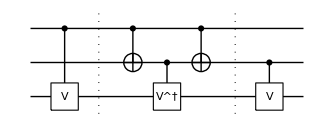

0

```mathematica
new1=QuantumCircuit[qc1,"Separator",qc2,"Separator",qc3]
qc-new1//Elaborate
```

```mathematica
new2=QuantumCircuit[qc3,"Separator",qc2,"Separator",qc1]
qc-new2//Elaborate
```

-Graphics-

0

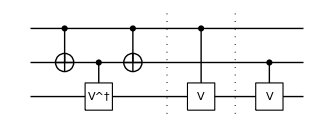

0

```mathematica
new3=QuantumCircuit[qc2,"Separator",qc1,"Separator",qc3]
qc-new3//Elaborate
```

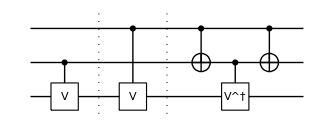

0

```mathematica
new4=QuantumCircuit[qc3,"Separator",qc1,"Separator",qc2]
qc-new4//Elaborate
```

The Fredkin Gate

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Closely related to the Toffoli gate is the Fredkin gate. The implementation of the Toffoli gate directly leads to that of the Fredkin gate. Furthermore, like the Toffoli gate, the Fredkin gate is universal for classical reversible computation but not universal for quantum computation.

The Fredkin gate “swaps” the states of the two target qubits when the control qubit is set in the state |1⟩, as depicted by the following two equivalent quantum circuit elements

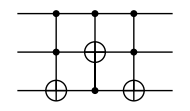
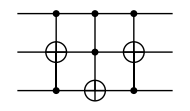
≡-Graphics-≡-Graphics-.

The equivalence of the two quantum circuits follows from the relation between the SWAP gate and the CNOT gate. In fact, the CNOT gate is the inverse of itself, and the above equivalent quantum circuit on the right-hand side can be further simplified as follows,

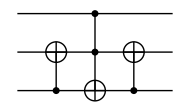
≡-Graphics-.

This equivalent quantum circuit was used by Smolin and DiVincenzo (1996) for an efficient implementation of the Fredkin gate in terms of the elementary gates . This is illustrated in the following demonstration .

### Demonstration

This shows the quantum circuit model of the quantum Fredkin gate.

```mathematica
qc=QuantumCircuit[Fredkin[S[1],S[2],S[3]]]
```

-Graphics-

This is an explicit operator expression of the Fredkin gate in terms of the Pauli operators.

```mathematica
op=Elaborate[qc]
```

3/4+1/4 S_2^x S_3^x+1/4 S_2^y S_3^y+1/4 S_2^z S_3^z-1/4 S_1^z S_2^x S_3^x-1/4 S_1^z S_2^y S_3^y-1/4 S_1^z S_2^z S_3^z+S_1^z/4

This is the matrix representation of the Fredkin gate in the logical basis.

```mathematica
mat=Matrix[qc];
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The Fredkin gate is equivalent to a combination of three Toffoli gates.

```mathematica
qc2=QuantumCircuit[
Toffoli[S[1],S[2],S[3]],
Toffoli[S[1],S[3],S[2]],
Toffoli[S[1],S[2],S[3]]]
```

-Graphics-

```mathematica
op2=Elaborate[qc2]
```

3/4+1/4 S_2^x S_3^x+1/4 S_2^y S_3^y+1/4 S_2^z S_3^z-1/4 S_1^z S_2^x S_3^x-1/4 S_1^z S_2^y S_3^y-1/4 S_1^z S_2^z S_3^z+S_1^z/4

```mathematica
op-op2
```

0

In fact, the relation between the SWAP gate and the CNOT gate suggests that there is another equivalent quantum circuit model of the Fredkin gate.

```mathematica
new=QuantumCircuit[
CNOT[S[3],S[2]],
Toffoli[S[1],S[2],S[3]],
CNOT[S[3],S[2]]
]
```

-Graphics-

```mathematica
qc-new//Elaborate
```

0

Implementations

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Let us now discuss how to implement the multi-control NOT gate in terms of the elementary gates. Here we introduce two methods that scale quadratically and linearly, respectively, with the number of qubits.

First, let us generalize the implementation in Figure 2 and Figure 3 of the Toffoli gate. Consider an n-control NOT gate, and examine the quantum circuit on the right-hand side of Figure 4. In the center piece between the dashed vertical lines of the quantum circuit, the unitary gate V^† operates only when either (not both) of all the first n−1 control qubits or the last control qubit is set to |1⟩. Therefore, putting V:=√X and combining this piece of quantum circuit with a controlled-V and (n−1)-control V gate lead to the desired n-control NOT gate. This implementation includes two (n−1)-control NOT gates, each of which requires, at least, 𝒪(n) elementary gates. It should recursively implement an (n−1)-control V gate as well, which requires, at least, 𝒪(n) elementary gates at each recursion. Overall, this implementation requires 𝒪(n^2) elementary gates.

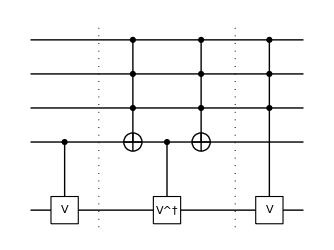
=-Graphics-

Figure 4. An implementation of the four-control NOT gate, where V:=√X. For an n-control NOT gate, it requires 𝒪(n^2) elementary gates.

Next, suppose that in the register, there are n−2 or more additional qubits that are not directly involved in the gate operation itself. In this case, one can use the properties of the Toffoli gate illustrated previously in Figure 1 and efficiently implement the n-control NOT gate using 4(n−2) Toffoli gates. This is shown in the quantum circuit on the right-hand side of Figure 5 for n=4 (Barenco et al., 1995). Since each Toffoli gate requires 5 elementary gates, the overall cost of this implementation scales as 𝒪(n).

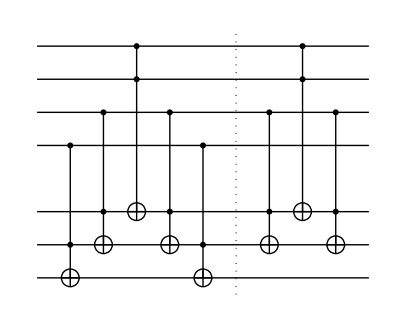
=-Graphics-

Figure 5. An implementation of the four-control NOT gate using eight Toffoli gates. For an n-control NOT gate, it requires 𝒪(n) elementary gates, and there must be n−2 other qubits available.

The latter implementation of a multi-control NOT gate uses additional qubits not directly involved in the gate operation itself. It is emphasized that the quantum states of the extra qubits should not be confused with the so-called “ancillary qubits” in the sense that they do not have to be initialized in a certain fixed quantum state and their state is not altered. The desired gate operation is performed properly regardless of the initial state of the extra qubits and their quantum state is restored after the gate operation. This is because we have put the second part after the vertical dashed line in the quantum circuit in Figure 5.

### Demonstration

For demonstration, consider an implementation of a 5-control NOT gate using 3 additional qubits.

```mathematica
$n=5;
$m=3;
cc=Range[$n];
aa=Range[$n+1,$n+$m];
tt=$n+$m+1;
```

This is the quantum circuit of a 5-control NOT gate.

```mathematica
qc=QuantumCircuit[CNOT[S[cc],S[tt]],"Visible"->S[aa]]
```

-Graphics-

Calculate the quantum circuit elements required for the implementation.

```mathematica
tofa=Table[Toffoli[S[$n-j+1],S[$n+$m-j+1],S[tt-j+1]],{j,1,$m}];
tofb=Toffoli[S[1],S[2],S[$n+1]];
tofc=Rest@tofa;
```

Here is the quantum circuit representation of the implementation. The second part after the vertical dashed line is to restore the additional qubits to their original states.

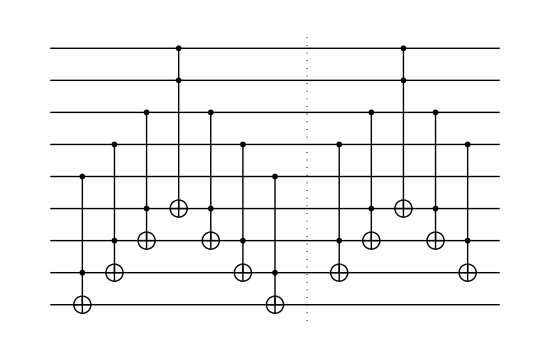

```mathematica
new=QuantumCircuit[Sequence@@Flatten@{tofa,tofb,Reverse@tofa,"Separator",tofc,tofb,Reverse@tofc}]
```

Check if the two quantum circuits are indeed equal. Note that due to the depth of the second quantum circuit new, it takes long to convert it to an operator expression, and Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol is much faster.

```mathematica
DeleteCases[Matrix[qc]-Matrix[new]//Flatten//Normal,0]
```

{}

| Related Guides
▪Quantum Computation and Quantum Information

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Computation and Quantum Information with Q3

| Related Links
▪A. Barenco, https://doi.org/10.1103/physreva.52.3457et al., Physical Review A 52 (5), 3457 (1995)https://doi.org/10.1103/physreva.52.3457, "Elementary gates for quantum computation."
▪J. A. Smolin and D. P. DiVincenzo, Physical Review A 53 (4), 2855 (1996)https://doi.org/10.1103/PhysRevA.53.2855, "Five two-bit quantum gates are sufficient to implement the quantum Fredkin gate." 
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).